```mathematica
ClearAll["Global`*"];
(* Rdb = 40 dB *)
R= 100; (* mean/side lobe ratio *)
nel = 7; (* number of elements *)
ℕ = (nel-1)/2;
ϵ0 = 8.854187*10^(-12); (* F*m^-1 vacuum permettivity *) 
μ0 = 1.256637*10^(-6);(* H*m^-1 vacuum permeability *)
ϵr = 1; (* relative permittivity *) 
μr = 1;  (* relative permeability *) 
ϵ = ϵ0*ϵr; (* medium permettivity *)
μ = μ0*μr; (* medium permeability *)
freq = 2.1*10^9; (* frequency in Hz *) 
Rdb[R_] := 20*Log[10, R];
x1[N_,R_] := FullSimplify[Cosh[(1/N)*ArcCosh[R]]];
LightSpeed[ϵ_,μ_] := 1/Sqrt[ϵ*μ];
LS = LightSpeed[ϵ,μ];
 λ = LS/freq;
x1 = x1[ℕ,R];
k0  = 2 π/λ; 
(* a, b coefficients for d ≤ λ/2 *) 
𝕒[d_] := (1+x1 Cos[k0 d])/(Cos[k0 d]-1);
𝕓[ d_] := -(1+x1)/(Cos[k0 d]-1);
(* a, b coefficients for d > λ/2 *) 
𝕒 = (x1-1)/2;
𝕓 = (x1+1)/2;
(* FullSimplify[D[a[d],d]] *) 
(*𝕒 = 𝕒[d]; 
𝕓 = 𝕓[d];*)
Print[Style["x1 is: ",Magenta],x1];
Print[Style["𝕒 is: ",Magenta],𝕒];
Print[Style["𝕓 is: ",Magenta],𝕓];
Print[Style["ℕ is: ", Magenta], ℕ];
(*d=λ/2;*)
Print["Done!"];
```

x1 is: Cosh[ArcCosh[100]/3]

𝕒 is: 1/2 (-1+Cosh[ArcCosh[100]/3])

𝕓 is: 1/2 (1+Cosh[ArcCosh[100]/3])

ℕ is: 3

Done!

{0.356083,{d→0.142758}}

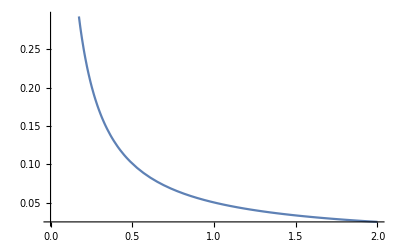

Done!

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→-0.0357434},{d→0.0357434}}

```mathematica
(* Inter element spacing optimization *) 
BWfn= 2 (π/2-ArcCos[ArcCos[Cos[π/(2 ℕ)-𝕒]/𝕓]/(k0 d)]);
BWfn°=BWfn*180/π;
FindMinimum[{BWfn, λ/2<d≤λ},d]
BWfnUnif[d_]:= (2 λ)/(nel d)*180/π  ;
BWfnUnif[d];
Plot[BWfn, {d, 0, 2}]
Print["Done!"];
Solve[Reduce[Cos[k0 d]== (1-𝕒)/𝕓],d]
```

```mathematica
(* COMPUTATION OF Feed Coefficients *) 
(* We use a T2, being nel = 5 *) 
ℂ0 = FullSimplify[4 𝕒^3+6 𝕒 𝕓^2-3 𝕒];
ℂ1 = FullSimplify[(12 𝕒^2 𝕓 + 3 𝕓^3-3 𝕓)/1];
ℂ2 = FullSimplify[6 𝕒 𝕓^2];
ℂ3 = FullSimplify[𝕓^3];
ηT=FullSimplify[1/nel*Abs[ℂ0+2 ℂ1+2 ℂ2+2ℂ3]^2/(ℂ0^2+2 ℂ1^2+2 ℂ2^2+2 ℂ3^2)];
Print[Style["ℂ0 is: ", Magenta], N[ℂ0,3]];
Print[Style["ℂ1 is: ", Magenta], N[ℂ1,3]];
Print[Style["ℂ2 is: ", Magenta], N[ℂ2,2]];
Print[Style["ℂ3 is: ", Magenta], N[ℂ3,2]];
Print[Style["Tapering Efficiency is: ", Magenta], PercentForm[N[ηT,2]]];
```

ℂ0 is: 25.3

ℂ1 is: 42.4

ℂ2 is: 24.

ℂ3 is: 8.1

Tapering Efficiency is: 79%